Confusion matrix (test set):

31 | 1 | 0
2 | 61 | 0

Overall accuracy = 0.968

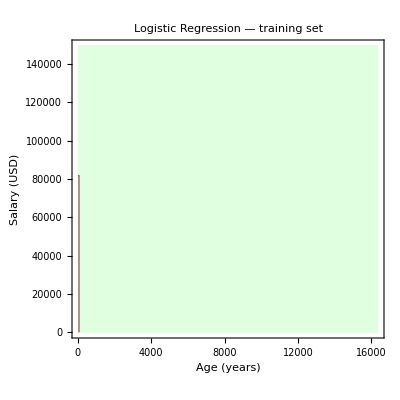

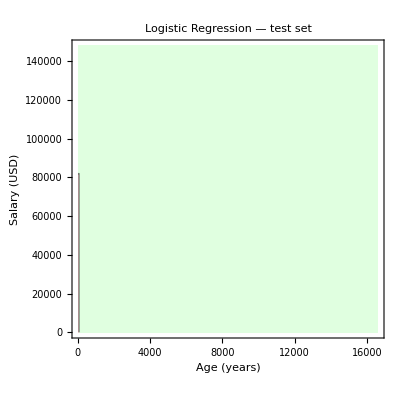

```mathematica
ClearAll["Global`*"];SeedRandom[0];
n=400;
ages=RandomInteger[{18,60},n];
salaries=RandomInteger[{15000,150000},n];
sigmoid[z_]:=1/(1+Exp[-z]);
logit=0.20 (ages-40)+0.00020 (salaries-60000);
probs=sigmoid/@logit;
labels=Boole[MapThread[#2<#1&,{probs,RandomReal[{0,1},n]}]];
rawExamples=MapThread[Association["Age"->#1,"Salary"->#2,"Purchased"->#3]&,{ages,salaries,labels}];
ratio=0.75;
trainMask=Thread[RandomReal[{0,1},n]<ratio];
trainData=Pick[rawExamples,trainMask,True];
testData=Pick[rawExamples,trainMask,False];
μ=Association["Age"->Mean[Lookup[trainData,"Age"]],"Salary"->Mean[Lookup[trainData,"Salary"]]];
σ=Association["Age"->StandardDeviation[Lookup[trainData,"Age"]],"Salary"->StandardDeviation[Lookup[trainData,"Salary"]]];
z[val_,key_]:=(val-μ[key])/σ[key];
standardise[ex_]:=Association["Age"->z[ex["Age"],"Age"],"Salary"->z[ex["Salary"],"Salary"],"Purchased"->ex["Purchased"]];
trainStd=standardise/@trainData;
testStd=standardise/@testData;
toPair[ex_]:=KeyTake[ex,{"Age","Salary"}]->ex["Purchased"];
trainPairs=toPair/@trainStd;
testPairs=toPair/@testStd;
clf=Classify[trainPairs,Method->"LogisticRegression"];
cm=ClassifierMeasurements[clf,testPairs,"ConfusionMatrix"];
acc=ClassifierMeasurements[clf,testPairs,"Accuracy"];
Print["Confusion matrix (test set):"];
Print[Grid[cm,Frame->All]];
Print["Overall accuracy = ",NumberForm[acc,{∞,3}]];
decisionPlot[data_,title_]:=Module[{pts,labs,pr,range,dens,g},pts=(Values[KeyTake[#1,{"Age","Salary"}]]&)/@data;labs=Lookup[data,"Purchased"];pr=({Min[#1]-1,Max[#1]+1}&)/@Transpose[pts];range=Thread[{pr⟦1⟧,pr⟦2⟧}];dens[x_,y_]:=clf[Association["Age"->z[x,"Age"],"Salary"->z[y,"Salary"]]];g=ContourPlot[dens[x,y],{x,Sequence@@range⟦1⟧},{y,Sequence@@range⟦2⟧},Contours->{0.5},ContourStyle->{Black,Thick},ColorFunction->(Blend[{LightRed,LightGreen},#1]&),PlotPoints->150,MaxRecursion->0,FrameLabel->{"Age (years)","Salary (USD)"},PlotRangePadding->None];Show[g,Graphics[MapThread[{EdgeForm[None],If[#2==1,Darker[Green,0.20],Darker[Red,0.20]],Disk[#1,.8]}&,{pts,labs}]],PlotLabel->Style[title,14,Bold],AspectRatio->1]];
trainingPlot=decisionPlot[trainData,"Logistic Regression — training set"];
testPlot=decisionPlot[testData,"Logistic Regression — test set"];
Print[trainingPlot];
Print[testPlot];
```

Training CM | ((0
0) | (0
0)
(0
0) | (0
0))
Test CM | ((0
0) | (0
0)
(0
0) | (0
0))

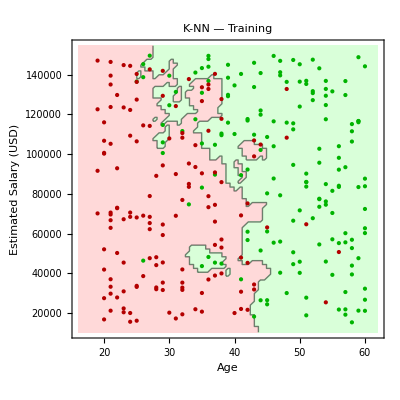

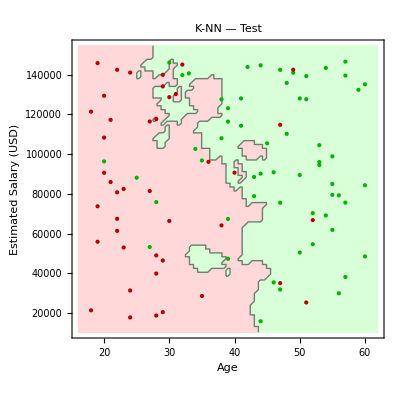

```mathematica
ClearAll["Global`*"];SeedRandom[123];
DarkGreen=Darker[Green,.3];
DarkRed=Darker[Red,.3];
n=400;
ages=RandomInteger[{18,60},n];
salaries=RandomInteger[{15000,150000},n];
sigmoid[z_]:=1/(1+Exp[-z]);
p=sigmoid[0.18 (ages-40)+0.00002 (salaries-60000)];
labels=Boole[Thread[RandomReal[{0,1},n]<p]];
data=Transpose[{ages,salaries}];
trainIdx=RandomSample[Range[n],Round[.75 n]];
testIdx=Complement[Range[n],trainIdx];
trainX=data⟦trainIdx⟧;trainY=labels⟦trainIdx⟧;
testX=data⟦testIdx⟧;testY=labels⟦testIdx⟧;
μ=Mean/@Transpose[trainX];
σ=StandardDeviation/@Transpose[trainX];
standardise[v_]:=MapThread[(#1-#2)/#3&,{v,μ,σ}];
trainXz=standardise/@trainX;
testXz=standardise/@testX;
k=5;
classifier=Classify[Thread[trainXz->trainY],Method->{"NearestNeighbors","NeighborsNumber"->k},PerformanceGoal->"Quality"];
trainPred=classifier/@trainXz;
testPred=classifier/@testXz;
cfm[truth_,pred_]:=Module[{c=Counts[Thread[{truth,pred}]]},{{Lookup[c,{0,0},0],Lookup[c,{0,1},0]},{Lookup[c,{1,0},0],Lookup[c,{1,1},0]}}];
Grid[{{"Training CM",MatrixForm[cfm[trainY,trainPred]]},{"Test CM",MatrixForm[cfm[testY,testPred]]}},Frame->All]
ageRange=MinMax[ages]+{-2,2};
salRange=MinMax[salaries]+{-5000,5000};
decision[a_,s_]:=classifier[standardise[{a,s}]];
plotSet[{ptsX_,ptsY_},title_]:=Show[ContourPlot[decision[x,y],{x,Sequence@@ageRange},{y,Sequence@@salRange},PlotPoints->75,MaxRecursion->0,AspectRatio->1,ColorFunction->(Blend[{{0,RGBColor[1,.85,.85]},{1,RGBColor[.85,1,.85]}},#1]&),Contours->{0.5},ContourStyle->Thick,FrameLabel->{"Age","Estimated Salary (USD)"},PlotLabel->title],Graphics[MapThread[{If[#2==1,DarkGreen,DarkRed],Point[#1]}&,{ptsX,ptsY}]],ImageSize->400];
trainPlot=plotSet[{trainX,trainY},"K-NN — Training"];
testPlot=plotSet[{testX,testY},"K-NN — Test"];
trainPlot
testPlot
```